```mathematica
动画演示“失步”现象
```

```mathematica
第一种方式(opt all pic and then press Ctrl+Y to animate it! )
```

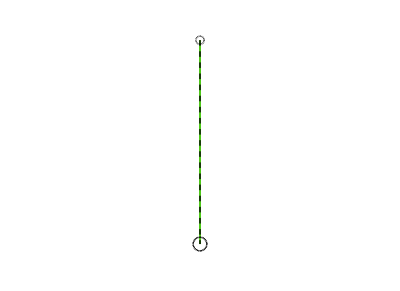

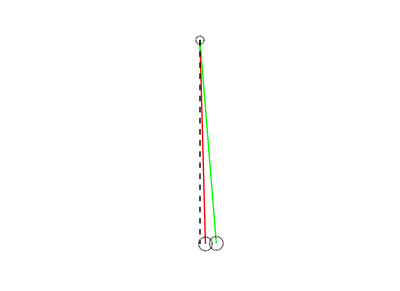

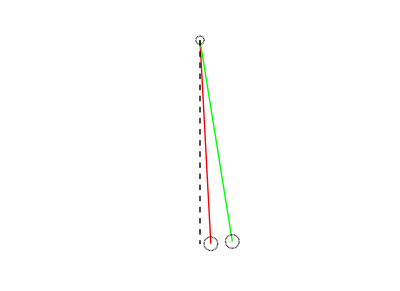

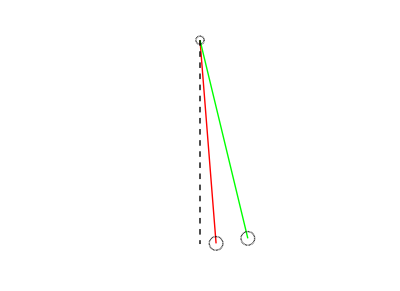

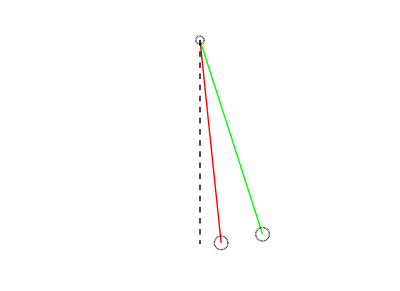

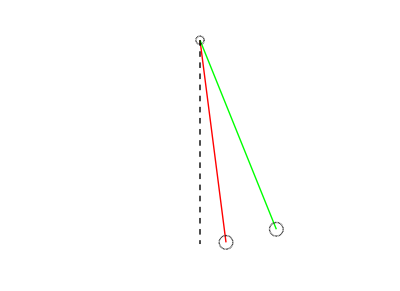

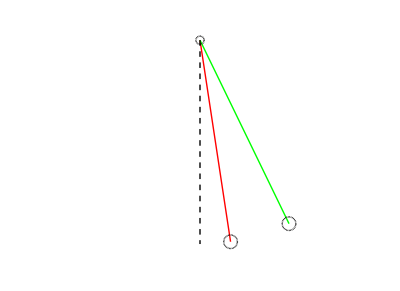

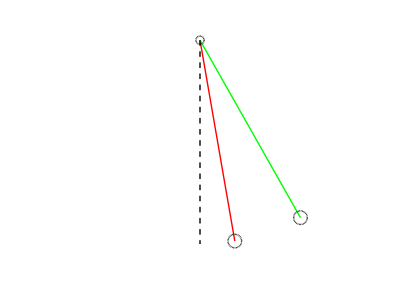

-Graphics-

-Graphics-

-Graphics-

«370 more identical outputs»

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v01=1;ω01=v01/L;   v02=3;ω02=v02/L;
as=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω01},θ,{t,0,20}];θ1=θ/.as[[1]];
bs=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω02},θ,{t,0,20}];θ2=θ/.bs[[1]];
n=500;δt=20/n;
Do[
({α1,α2}={θ1[t],θ2[t]}/.t->j*δt);
{x1,y1}=L*{Sin[α1],-Cos[α1]};
{x2,y2}=L*{Sin[α2],-Cos[α2]};
c=Show[
Graphics[{RGBColor[1,0,0],Line[{{0,0},{x1,y1}}],
RGBColor[0,1,0],Line[{{0,0},{x2,y2}}],
RGBColor[0,0,0],Dashing[{0.01}],
Line[{{0,0},{0,-L}}],Dashing[{0,0}],
Circle[{x1,y1},L/30],Circle[{x2,y2},L/30],
Circle[{0,0},L/50]}],AspectRatio->Automatic,
PlotRange->{{-0.8L,0.8L},{-1.1L,0.1}}];
Print[c],
{j,0,n}]
Clear[c,g,L,Ω,as,bs,n,δt,v01,v02,
ω01,ω02,θ1,θ2,α1,α2,x1,y1,x2,y2]
```

```mathematica
第二种方式
```

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v01=1;ω01=v01/L;   v02=3;ω02=v02/L;
as=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω01},θ,{t,0,20}];θ1=θ/.as[[1]];
bs=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω02},θ,{t,0,20}];θ2=θ/.bs[[1]];
Animate[
a=ListPlot[{{θ1[t],0}},PlotRange->π/4,
PlotStyle->{Orange,PointSize[0.03]}];
b=ListPlot[{{θ2[t],0}},PlotRange->π/4,
PlotStyle->{Black,PointSize[0.03]}];
Show[{a,b}],{t,0,20},ControlPlacement->Top]
Clear[a,b,g,L,Ω,as,bs]
```